```mathematica
FirstDataSet = ReadList["C:\\Users\\Администратор\\Desktop\\krs\\FirstDataSet.txt",{Number,Number}];
SecondDataSet = ReadList["C:\\Users\\Администратор\\Desktop\\krs\\SecondDataSet.txt",{Number,Number}];
```

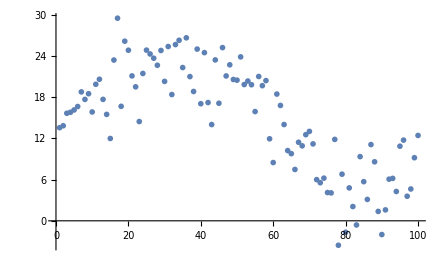

```mathematica
ListPlot[SecondDataSet]
```

```mathematica
CoreQuart[r_] := (
If[r > 1, 0, (1 - r^2)^2]
);
CoreOpt[r_] := (
If[r > 1, 0, (1 - r^2)]
);
CoreRect[r_] := (
If[r > 1, 0, 0.5]
);
K[xx_,xxi_, hh_] := (

CoreOpt[Abs[xx - xxi] / hh]

);

RegressionFormula[x_, DataSet_, h_] := (

verh = Sum[DataSet[[i,2]]*K[x,DataSet[[i,1]], h],{i, 1 Length[DataSet]}];
niz = Sum[K[x,DataSet[[i,1]], h],{i, 1 Length[DataSet]}];

verh / niz
);
```

```mathematica
ApproximationError[xx_,DataSetA_, h_] := (

ll2 = Length[DataSetA];
res =(RegressionFormula[xx, DataSetA, h] - DataSetA[[i,2]])^2;

res
);

hDynamic = {};

OptH[DataSet_] := Module[
{probablyH, result,deleteNum, temporaryDataSet, hSum, minH = 1.1, minValue}
,

For[probablyH = 1.1, probablyH ≤ 30, probablyH += 0.1,
(*PrintTemporary[probablyH];*)
ll = Length[DataSet] ;

hSum = Sum[(RegressionFormula[DataSet[[icounter,1]], Delete[DataSet,icounter], probablyH] - DataSet[[icounter,2]])^2, {icounter, 1, ll}]/ll;

If[hSum < Sum[(RegressionFormula[DataSet[[icounter,1]], Delete[DataSet,icounter], minH] - DataSet[[icounter,2]])^2, {icounter, 1, ll}]/ll,
minH = probablyH;
];

AppendTo[hDynamic,{probablyH,hSum}];

];

minH
];
```

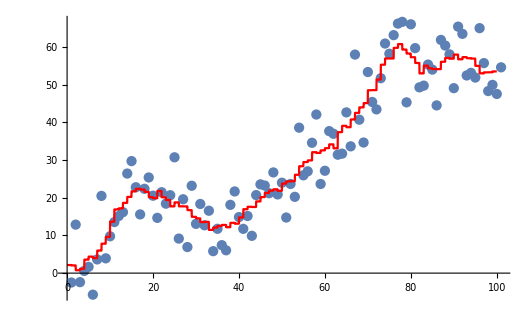

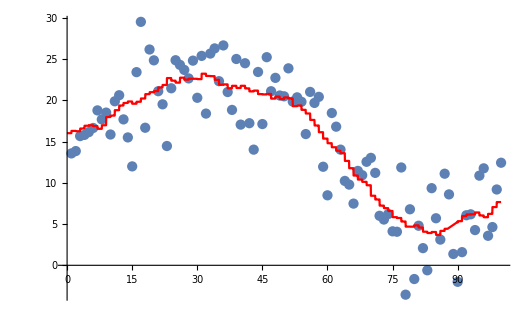

```mathematica
h1 = OptH[FirstDataSet];
h2 = OptH[SecondDataSet];
Show[ListPlot[FirstDataSet], Plot[RegressionFormula[x, FirstDataSet, h1], {x, 0, 100}, PlotStyle->{Red}]]
Show[ListPlot[SecondDataSet], Plot[RegressionFormula[x, SecondDataSet, h2], {x, 0, 100}, PlotStyle->{Red}]]
```

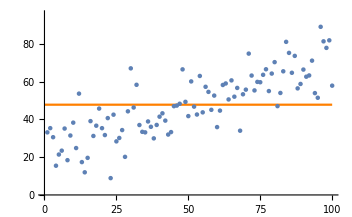

```mathematica
Show[ Plot[RegressionFormula[x, FirstDataSet, 5000000000], {x, 0, 100}, PlotStyle->{Orange}],ListPlot[FirstDataSet]]
```

```mathematica
hDynamic={};
OptH[SecondDataSet];
```